## MAT 331: Homework 3

## Problem 3.1

The replacement operator /. (slash-dot) applies a transformation rule to an expression. If you give a list of rules, each rule will be tried once on each part of the expression. If you give a list of lists of rules, you get a list of results; each sublist is treated like an independent set of rules.

```mathematica
x^2+x^3+y^2+z /. x->2
```

12+y^2+z

```mathematica
x^2+x^3+y^2+z /. {x->2, y->3, z->1}
```

22

```mathematica
x^2+x^3+y^2+z /. {{x->2},{x^2->2, y->3,z->1},{x->0,z->0}}
```

{12+y^2+z,12+x^3,y^2}

```mathematica
x^2+x^3+y^2+z /. {x_^n_ -> a}
```

3 a+z

Write a replacement rule that when applied to the expression f[x] + g[x] outputs Sin[x] + Cos[3].

```mathematica
f[x]+g[x]/.{f[x]->Sin[x], g[x]->Cos[3]}
```

Cos[3]+Sin[x]

Write a transformation rule that replaces any expression of the form Function[variable] with Cos[3].

```mathematica
f[x]+g[y]+h[z]/.{f_[x_]->Cos[3]}
```

3 Cos[3]

## Problem 3.2

Mathematica can solve various kinds of equations, symbolically or numerically. The result will be displayed as a list of transformation rules. We can then use the replacement operator /. (slash-dot) to apply these rules to any gven expression.

Use the command Solve[x^2+ 2a x + b==0, x] to find the roots of the quadratic polynomial x^2+ 2 a x + b. You do not need to give numerical values to the coefficients a and b.

```mathematica
Solve[x^2+2*a*x+b==0,x]
```

{{x→-a-√(a^2-b)},{x→-a+√(a^2-b)}}

Find the sum of the roots of the polynomial and the product of the roots of the polynomial using the replacement operator. Check that Viète’s relations are satisfied (i.e. the sum of the roots is equal to -2a and the product is equal to b). You may need to use the command Simplify[...] as well.

```mathematica
Replace[u+w,u+w->-a-√(a^2-b)+-a+√(a^2-b)]
```

-2 a

```mathematica
Replace[u*w,u*w->(-a-√(a^2-b))*(-a+√(a^2-b))]
```

(-a-√(a^2-b)) (-a+√(a^2-b))

```mathematica
Simplify[(-a-√(a^2-b)) (-a+√(a^2-b))]
```

b

The sum of the Roots is equal to -2a and the product is equal to b.

Consider now the cubic polynomial x^3+ax^2+bx+c. Use Mathematica to find the roots x_1, x_2 and x_3. Then use transformation rules to compute the three symmetric expressions x_1+x_2+x_3, x_1x_2+x_2x_3+x_3x_1 and x_1x_2x_3. Use Simplify[...] to simplify the computations. What can you conclude about the relation between the three expressions and the coefficients of the polynomial?

```mathematica
Solve[x^3+a*x^2+b*x+c==0,x]
```

{{x→-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3))},{x→-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))},{x→-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}}

```mathematica
u+v+w/.{u->-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3)),v->-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)),w->-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}
```

-a-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))

```mathematica
Simplify[%37]
```

-a

```mathematica
u*v+u*w+v*w/.{u->-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3)),v->-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)),w->-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}
```

(-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3))) (-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+3+3 √3 √(-a^2 b^2+4 b^3+1-1+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)))+(-a/3-1+1/(3 1)) 1+(-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+3+1)^(1/3))-((1-ⅈ √3) (-2 a^3+3+3 √3 √1)^(1/3))/(6 2^(1/3))) (-a/3+((1-ⅈ √3) (1))/(3 2^1 1)-((1+ⅈ √3) (1)^(1/3))/(6 2^(1/3)))
 |  |  |  |

```mathematica
Simplify[%32]
```

b

```mathematica
u*v*w/.{u->-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3)),v->-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)),w->-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}
```

(-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3))) (-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))) (-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)))

```mathematica
Simplify[%39]
```

-c

If ax3+bx2+cx+d=0 ,then x1x2x3=-d/a ，x1x2+x1x3+x2x3=c/a ，x1+x2+x3=-b/a
we can check, in this case, a=1 b=a, c=b ,d=c.  x1x2x3=-c/1=-c ，x1x2+x1x3+x2x3=b/1=b ，x1+x2+x3=-a/1=-a the same as what we got.

## Problem 3.3

Consider the differential equation y'(x) = 1+y(x). Use VectorPlot[ ...] and StreamPlot[ ...] to plot the vector field of the differential equation. Try several display options (i.e. change the size of the arrows, make the picture larger, change the colors, etc.)

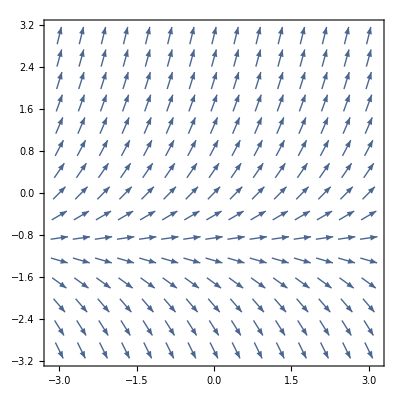

```mathematica
VectorPlot[{1,1+y},{x,-3,3},{y,-3,3},VectorScale->{Tiny,Small,None}]
```

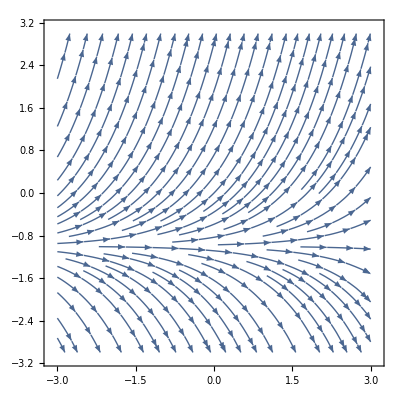

```mathematica
StreamPlot[{1,1+y},{x,-3,3},{y,-3,3}]
```

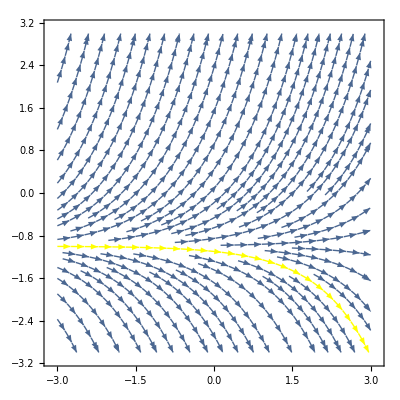

```mathematica
StreamPlot[{1,1+y},{x,-3,3},{y,-3,3},StreamScale->Tiny,StreamPoints->{{{{0,-1.1},Yellow}, Automatic}}]
```

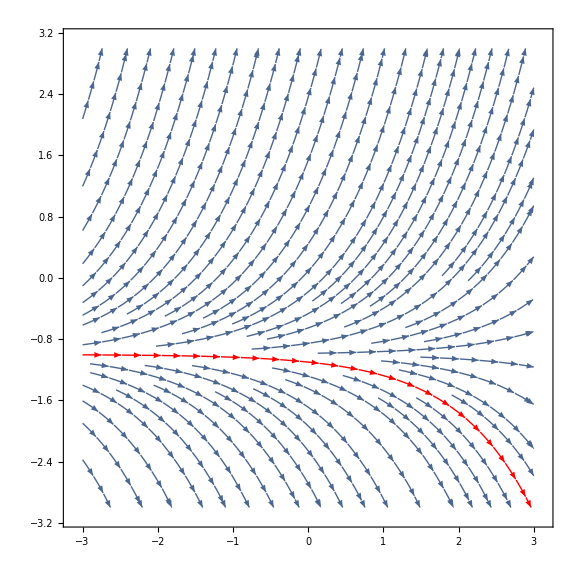

```mathematica
Show[%5,ImageSize->Large]
```

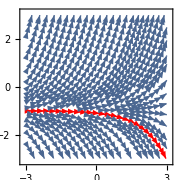

```mathematica
Show[%6,ImageSize->Small]
```

```mathematica
Show[%7,Axes->True,AxesStyle->Black]
```

-Graphics-

Next use DSolve[...] to solve the differential equation y’(x) = 1+y(x), with initial condition y(0)=1. The result will be a list of replacement rules. Define a function YSol[x_] that returns the solution found by DSolve[...]. Evaluate YSol numerically at x=0 and x=0.1. Then plot the function YSol.

```mathematica
sol1=DSolve[{y'[x]==1+y[x],y[0]==1},y[x],x]
```

{{y[x]→-1+2 ⅇ^x}}

```mathematica
YSol[x_]= y[x] /. Flatten[sol1]
```

-1+2 ⅇ^x

```mathematica
YSol[0]
```

1

```mathematica
YSol[0.1]
```

1.21034

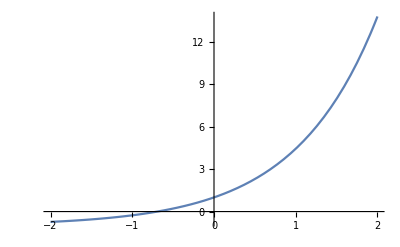

```mathematica
Plot[YSol[x],{x,-2,2},PlotRange->All]
```

## Problem 3.4

Use the condition operator /; (slash-semicolon) to define a function F1 that is -x-1 if x<1, √(1-x^2) if -1⩽x⩽1 and x-1 if x>1. Plot the function on the interval [-3,3] and color the region between the graph of F1 and the x-axis. Then plot F1 together with the function Abs[x]-1 on the same graph.

Define a function fsum[x_] that returns the sum of the elements from x. If x is a number, then it returns x. If x is a vector, like {1,2,3}, fsum returns the sum of the elements of the vector (6 in this case). If x is a matrix, then the function should return the sum of the elements of the matrix.

Note : From time to time, you may need to clear previous definitions; to clear previous definitions of f use Clear[f].

```mathematica
F1[x_]:=-x-1/;x<-1
F1[x_]:=√(1-x^2)/;-1≤x≤1
F1[x_]:=x-1/;x>1
```

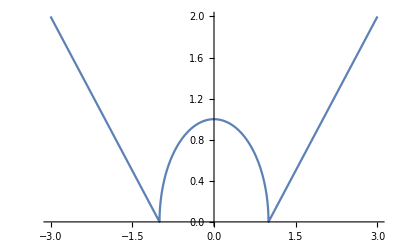

```mathematica
Plot[F1[x],{x,-3,3}]
```

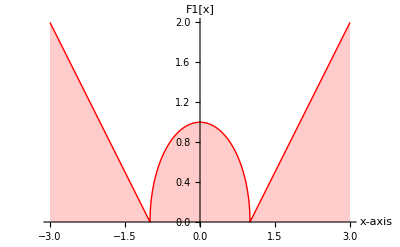

```mathematica
Plot[F1[x],{x,-3,3},AxesLabel->{"x-axis","F1[x]"},PlotStyle->{Red,Thick},Filling->Axis]
```

```mathematica
F2[x_]:=Abs[x]-1
```

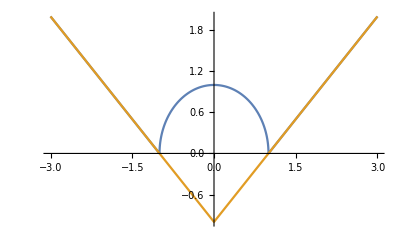

```mathematica
Plot[{F1[x],F2[x]},{x,-3,3}]
```

```mathematica
fsum[x_]:=x/;NumberQ[x]
fsum[x_]:=Module[{i,len, sum},len=Length[x];sum=0;
For[i=1, i≤len, i++, sum = sum+x[[i]]];Return[sum]]
```

```mathematica
fsum[{3,5,7,20}]
```

35

```mathematica
fsum[5]
```

5

counting sum for n*n matrix:

```mathematica
fsum[x_]:=Module[{i,j,len,sumelement},len=Length[x];sumelement=0;
For[i=1,i≤len,i++,For[j=1,j≤len,j++,sumelement=sumelement+x[[i,j]]]];
sumelement];
```

```mathematica
A={{1,2,3},{3,4,5},{4,5,6}}
fsum[A]
```

{{1,2,3},{3,4,5},{4,5,6}}

33

counting sum for any m*n matrix:

```mathematica
fsum[x_]:=(x//Flatten//Total)
B={{1,2,3,7},{3,4,5,8},{4,5,6,9}}
```

```mathematica
fsum[B]
```

57

## Problem 3.5

The symbol /@ (slash-at) is used in Mathematica as a shorthand notation for Map[...], as described in the lecture notes. This is useful whenever we want to map a function to a list, without using any loops.

```mathematica
G /@ {1,2,3,4,5,6,7,8,9,10}
```

{G[1],G[2],G[3],G[4],G[5],G[6],G[7],G[8],G[9],G[10]}

Note that this is in general different from G[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}], which takes as argument the given list.

```mathematica
G[{1,2,3,4,5,6,7,8,9,10}]
```

G[{1,2,3,4,5,6,7,8,9,10}]

Most built-in Mathematica functions act on lists element-by-element. See for example the trigonometric functions. That is, Mathematica typically maps functions across lists. Such functions have the Attribute Listable. If you want to give this attribute to your own function f, type SetAttributes[f,Listable].

```mathematica
SetAttributes[G,Listable];
G[{1,2,3,4,5,6,7,8,9,10}]
```

{G[1],G[2],G[3],G[4],G[5],G[6],G[7],G[8],G[9],G[10]}

The symbol @ (slash) maps a function (of one argument) to its argument. In place of writing f[x], one could simply write f @ x. With @ you do not have to move to the end of the expression to match the square bracket. You can also use the // postfix notation to accomplish the same thing.

```mathematica
MatrixForm @ {{1,2,3},{4,5,6}}
```

(1 | 2 | 3
4 | 5 | 6)

```mathematica
{{1,2,3},{4,5,6}} // MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

The symbol @@ (slash-slash) applies a function (of several arguments) to its arguments.

```mathematica
G @@ {1,2,3,4}
```

G[1,2,3,4]

#### Questions:

Decide whether /@, @, @@ and // have low or high precedence. For example, does x+y // f  mean x+f[y] or f[x+y]? Is f @ x+y equivalent to f[x]+y or to f[x+y]? How about f+g /@ {1,2,3} and f+g @@ {1,2,3}?

```mathematica
x+y//f
```

f[x+y]

```mathematica
f@x+y
```

y+f[x]

```mathematica
f+g/@{1,2,3}
```

{f+g[1],f+g[2],f+g[3]}

```mathematica
f+g@@{1,2,3}
```

f+g[1,2,3]

// has low precedence.  @, /@ and @@ have high precedence.

Using only the shortand notation @ write a composition of functions f(g(h(x))). Using only the shorthand notation @@, write a composition of functions f(g(h(x))).

```mathematica
f@g@h[x]
```

f[g[h[x]]]

```mathematica
f@@{g@@{h[x]}}
```

f[g[h[x]]]

Using only shorthand notations, map the function F1 from problem 3.4 to the list {-3,-2,1,0,1,2,3}. Next make the function F1 listable and compute F1[{-3,-2,1,0,1,2,3}].

```mathematica
F1/@{-3,-2,-1,0,1,2,3}
```

{F1[-3],F1[-2],F1[-1],F1[0],F1[1],F1[2],F1[3]}

```mathematica
SetAttributes[F1,Listable];
F1[{-3,-2,1,0,1,2,3}]
```

{F1[-3],F1[-2],F1[1],F1[0],F1[1],F1[2],F1[3]}

```mathematica
Clear[F1]
```

```mathematica
F1[x_]:=-x-1/;x<-1
F1[x_]:=√(1-x^2)/;-1≤x≤1
F1[x_]:=x-1/;x>1
```

```mathematica
F1[{-3,-2,1,0,1,2,3}]
```

{2,1,0,1,0,1,2}